```mathematica
Clear[g,gg, a]
a = 1;
g=Array[gg[#1, #2]&,{3,3}]/.gg[i_, i_]->1/.gg[i_, j_]->-lmb;
q = {q0, q1, q2};
G = Inverse[g] - DiagonalMatrix[b(1-q)];
MatrixForm[G]
IG = Inverse[G];
p[b_, lmb_,q0_,q1_,q2_]=-Sum[√(q[[d]]/q[[a]])*G[[a,d]] Boole[d!=a],{d,3}]-Sum[√(q[[d]]*q[[c]])D[IG[[d, c]],q0],{d, 3}, {c, 3}];
```

((-1+lmb)/(-1+lmb+2 lmb^2)-b (1-q0) | -lmb/(-1+lmb+2 lmb^2) | -lmb/(-1+lmb+2 lmb^2)
-lmb/(-1+lmb+2 lmb^2) | (-1+lmb)/(-1+lmb+2 lmb^2)-b (1-q1) | -lmb/(-1+lmb+2 lmb^2)
-lmb/(-1+lmb+2 lmb^2) | -lmb/(-1+lmb+2 lmb^2) | (-1+lmb)/(-1+lmb+2 lmb^2)-b (1-q2))

True

```mathematica
Clear[a, p, psimp, part0, parts, part00, partzinha]
a = 1;
part0[b_, lmb_,q0_,q1_,q2_]=-Sum[√(q[[1]]*q[[1]])D[IG[[1, 1]],q0],{i, 1}];
part00[b_, lmb_,q0_,q1_,q2_]=-√(q[[1]]*q[[1]])D[IG[[1, 1]],q0];
parts[b_, lmb_,q0_,q1_,q2_]=-Array[√(q[[#1]]*q[[#2]])D[IG[[#1, #2]],q[[a]]]&,{3, 3}];
-√(q[[1]]*q[[1]])D[IG[[1, 1]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
part0[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
part00[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
(*-√(q[[1]]*q[[2]])D[IG[[1, 2]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
-√(q[[1]]*q[[3]])D[IG[[1, 3]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
-√(q[[2]]*q[[1]])D[IG[[2, 1]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
-√(q[[2]]*q[[2]])D[IG[[2, 2]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
-√(q[[2]]*q[[3]])D[IG[[2, 3]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
-√(q[[3]]*q[[1]])D[IG[[3, 1]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
-√(q[[3]]*q[[2]])D[IG[[3, 2]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
-√(q[[3]]*q[[3]])D[IG[[3, 3]],q[[a]]]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}*)
```

8.03717×10^10

8.03717×10^10

8.03717×10^10

```mathematica
Simplify[parts[b, lmb,q0,q1,q2][[2, 2]]==parts[b, lmb,q0,q2,q1][[3, 3]]]
Simplify[parts[b, lmb,q0,q1,q2][[2, 3]]==parts[b, lmb,q0,q2,q1][[3, 2]]]
Simplify[parts[b, lmb,q0,q1,q2][[3, 2]]==parts[b, lmb,q0,q2,q1][[2, 3]]]
Simplify[parts[b, lmb,q0,q1,q2][[3, 3]]==parts[b, lmb,q0,q2,q1][[2, 2]]]
Simplify[parts[b, lmb,q0,q1,q2][[1, 3]]==parts[b, lmb,q0,q2,q1][[1, 2]]]
Simplify[parts[b, lmb,q0,q1,q2][[1, 2]]==parts[b, lmb,q0,q2,q1][[1, 3]]]
Simplify[part0[b, lmb,q0,q1,q2]==part0[b, lmb,q0,q2,q1]]
```

True

True

True

«3 more identical outputs»

```mathematica
Clear[p1, p2, p3, p4]
p1 = parts[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526};
p2 = parts[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.13533526,q2->0.413916};
p1 //MatrixForm
p2//MatrixForm
p3 = parts[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->9/10,q1->4/10,q2->1/10};
p4 = parts[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->9/10,q1->1/10,q2->4/10};
N[p3]//MatrixForm[p3]
N[p4]//MatrixForm
```

(8.03717×10^10 | 1.30171×10^9 | 4.76341×10^8
1.30171×10^9 | 2.10826×10^7 | 7.71486×10^6
4.76341×10^8 | 7.71486×10^6 | 2.82314×10^6)

(8.03717×10^10 | 4.76341×10^8 | 1.30171×10^9
4.76341×10^8 | 2.82314×10^6 | 7.71486×10^6
1.30171×10^9 | 7.71486×10^6 | 2.10826×10^7)

(369062521/29929 | 17097790/89787 | 5379080/89787
17097790/89787 | 792100/269361 | 249200/269361
5379080/89787 | 249200/269361 | 78400/269361)[{{12331.3,190.426,59.9093},{190.426,2.94066,0.925152},{59.9093,0.925152,0.291059}}]

(12331.3 | 59.9093 | 190.426
59.9093 | 0.291059 | 0.925152
190.426 | 0.925152 | 2.94066)

```mathematica
ptrouble= part0[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
Total[p1, 2]
```

```mathematica
N[p[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->9/10,q1->1/10,q2->4/10}]
N[p[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->89728182/100000000,q1->413916/1000000,q2->13533526/100000000}]
part00[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}
 parts[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->0.89728182,q1->0.413916,q2->0.13533526}//MatrixForm
```

12836.9

8.39671×10^10

8.03717×10^10

```mathematica
Volume[ImplicitRegion[p[10, 0.2,q0,q1,q2]<=1,{{q0,0.01,0.99},{q1,0.01,0.99},{q2,0.01,0.99}}]]
```

$Aborted

```mathematica
Plot3D[p[10, 0.1,0.7,q1,q2],{q1,0,1},{q2, 0, 1},AxesLabel->Automatic, PlotRange->Full]
Plot3D[p[10, 0.1,0.75,q1,q2],{q1,0,1},{q2, 0, 1},AxesLabel->Automatic, PlotRange->Full]
Plot3D[p[10, 0.1,0.8,q1,q2],{q1,0,1},{q2, 0, 1},AxesLabel->Automatic, PlotRange->Full]
Plot3D[p[10, 0.1,0.85,q1,q2],{q1,0,1},{q2, 0, 1},AxesLabel->Automatic, PlotRange->Full]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
RegionPlot3D[p[5, 0,q1,q2,q3]>10^2,{q1,0.01,0.99},{q2,0.01,0.99},{q3,0.01,0.99}]
RegionPlot3D[p[5, 0.1,q1,q2,q3]>10^2,{q1,0.01,0.99},{q2,0.01,0.99},{q3,0.01,0.99}]
RegionPlot3D[p[5, 0.2,q1,q2,q3]>10^2,{q1,0.01,0.99},{q2,0.01,0.99},{q3,0.01,0.99}]
RegionPlot3D[p[5, 0.3,q1,q2,q3]>10^2,{q1,0.01,0.99},{q2,0.01,0.99},{q3,0.01,0.99}]
RegionPlot3D[p[5, 0.4,q1,q2,q3]>10^3,{q1,0.01,0.99},{q2,0.01,0.99},{q3,0.01,0.99}]
N[p[b, lmb,q0,q1,q2]/.{b->10, lmb->1/10, q0->9/10,q1->1/10,q2->4/10}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

12836.9

```mathematica
Plot3D[p[10, 0.1,q1,0.7,q2],{q1,0,1},{q2, 0, 1},AxesLabel->Automatic, PlotRange->Full]
Plot3D[p[10, 0.1,q1,0.75,q2],{q1,0,1},{q2, 0, 1},AxesLabel->Automatic, PlotRange->Full]
Plot3D[p[10, 0.1,q1,0.8,q2],{q1,0,1},{q2, 0, 1},AxesLabel->Automatic, PlotRange->Full]
Plot3D[p[10, 0.1,q1,0.85,q2],{q1,0,1},{q2, 0, 1},AxesLabel->Automatic, PlotRange->Full]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

```mathematica
swap[b_, lmb_,q0_,q1_,q2_]=p[b, lmb,q0,q1,q2]-p[b, lmb,q0,q2,q1];
swapsimp = Simplify[swap[b, lmb,q0,q1,q2], Assumptions->{0<=q0<=1, 0<=q1<=1, 0<=q2<=1, b>0, lmb>=0}]
```

0

```mathematica
Simplify[p[b, lmb,q0,q1,q2], Assumptions->{0<=q0<=1, 0<=q1<=1, 0<=q2<=1, b>0, lmb-0}]
```

$Aborted

```mathematica
swapsimp/.{b->10, lmb->1/10, q0->9/10,q1->1/10,q2->4/10}
```

-2949185296934283750/2793973497438659041

```mathematica
psimp = Simplify[p[b, 0,q0,q1,q2], Assumptions->{0<=q0<=1, 0<=q1<=1, 0<=q2<=1, b>0, lmb->0}]
```

(b q0)/(1+b (-1+q0))^2

```mathematica
psimp1 = psimp /.{b->10, lmb->0.1, q0->0.89728182,q1->0.413916,q2->0.13533526};
psimp2 = psimp /.{b->10, lmb->0.1, q0->0.89728182,q1->0.13533526,q2->0.413916};
psimp1 - psimp2
```

1.47822

```mathematica
pp=p/.β->b/.λ->lmb/.q[0]->q0/.q[1]->q1/.q[2]->q2;
FullSimplify[pp, Assumptions->{-1<q0<1, -1<q1<1, -1<q2<1, Element[b, Reals], Element[lmb, Reals]}]
```

(b (-1+lmb+2 lmb^2)^3 √(q0^2) (lmb^2-(1-lmb-b (-1+lmb+2 lmb^2) (-1+q1)) (1-lmb-b (-1+lmb+2 lmb^2) (-1+q2)))^2-2 b lmb (-1+2 lmb) (-1+lmb+2 lmb^2)^3 √(q0 q1) (lmb^2-(1-lmb-b (-1+lmb+2 lmb^2) (-1+q1)) (1-lmb-b (-1+lmb+2 lmb^2) (-1+q2))) (1+b (1+lmb) (-1+q2))+b (1-2 lmb)^2 lmb^2 (-1+lmb+2 lmb^2)^3 √(q1^2) (1+b (1+lmb) (-1+q2))^2-2 b lmb (-1+2 lmb) (-1+lmb+2 lmb^2)^3 (1+b (1+lmb) (-1+q1)) (lmb^2-(1-lmb-b (-1+lmb+2 lmb^2) (-1+q1)) (1-lmb-b (-1+lmb+2 lmb^2) (-1+q2))) √(q0 q2)+2 b (1-2 lmb)^2 lmb^2 (-1+lmb+2 lmb^2)^3 (1+b (1+lmb) (-1+q1)) (1+b (1+lmb) (-1+q2)) √(q1 q2)+b (1-2 lmb)^2 lmb^2 (-1+lmb+2 lmb^2)^3 (1+b (1+lmb) (-1+q1))^2 √(q2^2)+lmb √(q1/q0) (-1+3 lmb-4 lmb^3+b^3 (-1+lmb+2 lmb^2)^3 (-1+q0) (-1+q1) (-1+q2)-b (1-2 lmb)^2 (1+lmb) (-3+q0+q1+q2)+b^2 (-1+lmb) (-1+lmb+2 lmb^2)^2 (3-2 q1+(-2+q1) q2+q0 (-2+q1+q2)))^2+lmb √(q2/q0) (-1+3 lmb-4 lmb^3+b^3 (-1+lmb+2 lmb^2)^3 (-1+q0) (-1+q1) (-1+q2)-b (1-2 lmb)^2 (1+lmb) (-3+q0+q1+q2)+b^2 (-1+lmb) (-1+lmb+2 lmb^2)^2 (3-2 q1+(-2+q1) q2+q0 (-2+q1+q2)))^2)/((-1+lmb+2 lmb^2) (-1+3 lmb-4 lmb^3+b^3 (-1+lmb+2 lmb^2)^3 (-1+q0) (-1+q1) (-1+q2)-b (1-2 lmb)^2 (1+lmb) (-3+q0+q1+q2)+b^2 (-1+lmb) (-1+lmb+2 lmb^2)^2 (3-2 q1+(-2+q1) q2+q0 (-2+q1+q2)))^2)

```mathematica
ppp=(β (-1+λ+2 λ^2)^3 √(q[1]^2) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3])))^2-2 β λ (-1+2 λ) (-1+λ+2 λ^2)^3 √(q[1] q[2]) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3]))) (1+β (1+λ) (-1+q[3]))+β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 √(q[2]^2) (1+β (1+λ) (-1+q[3]))^2-2 β λ (-1+2 λ) (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2])) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3]))) √(q[1] q[3])+2 β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2])) (1+β (1+λ) (-1+q[3])) √(q[2] q[3])+β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2]))^2 √(q[3]^2)+λ √(q[2]/q[1]) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2+λ √(q[3]/q[1]) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2)/((-1+λ+2 λ^2) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2)
```

(β (-1+λ+2 λ^2)^3 √(q[1]^2) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3])))^2-2 β λ (-1+2 λ) (-1+λ+2 λ^2)^3 √(q[1] q[2]) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3]))) (1+β (1+λ) (-1+q[3]))+β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 √(q[2]^2) (1+β (1+λ) (-1+q[3]))^2-2 β λ (-1+2 λ) (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2])) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3]))) √(q[1] q[3])+2 β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2])) (1+β (1+λ) (-1+q[3])) √(q[2] q[3])+β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2]))^2 √(q[3]^2)+λ √(q[2]/q[1]) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2+λ √(q[3]/q[1]) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2)/((-1+λ+2 λ^2) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2)

```mathematica
ppp = pp/.q[1]->q[0]/.q[2]->q[1]/.q[3]->q[1];
ppp-p//FullSimplify
```

$Aborted

```mathematica
(β (-1+λ+2 λ^2)^3 √(q[1]^2) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3])))^2-2 β λ (-1+2 λ) (-1+λ+2 λ^2)^3 √(q[1] q[2]) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3]))) (1+β (1+λ) (-1+q[3]))+β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 √(q[2]^2) (1+β (1+λ) (-1+q[3]))^2-2 β λ (-1+2 λ) (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2])) (λ^2-(1-λ-β (-1+λ+2 λ^2) (-1+q[2])) (1-λ-β (-1+λ+2 λ^2) (-1+q[3]))) √(q[1] q[3])+2 β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2])) (1+β (1+λ) (-1+q[3])) √(q[2] q[3])+β (1-2 λ)^2 λ^2 (-1+λ+2 λ^2)^3 (1+β (1+λ) (-1+q[2]))^2 √(q[3]^2)+λ √(q[2]/q[1]) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2+λ √(q[3]/q[1]) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2)/((-1+λ+2 λ^2) (-1+3 λ-4 λ^3+β^3 (-1+λ+2 λ^2)^3 (-1+q[1]) (-1+q[2]) (-1+q[3])-β (1-2 λ)^2 (1+λ) (-3+q[1]+q[2]+q[3])+β^2 (-1+λ) (-1+λ+2 λ^2)^2 (3-2 q[2]+(-2+q[2]) q[3]+q[1] (-2+q[2]+q[3])))^2)
```

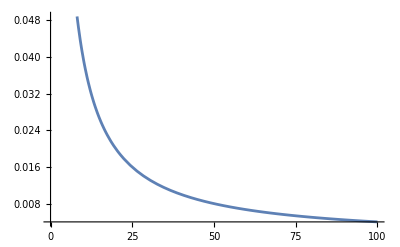

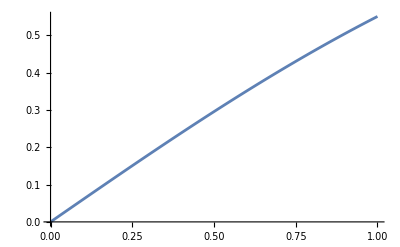

```mathematica
coshint [m_, p_]:=NIntegrate[Exp[-x^2/2]*Tanh[m+p*x],{x,-Infinity, Infinity}]/√(2π);
Plot[coshint[1/2, p],{p,0,100}]
Plot[coshint[m, 1],{m,0,1}]
```

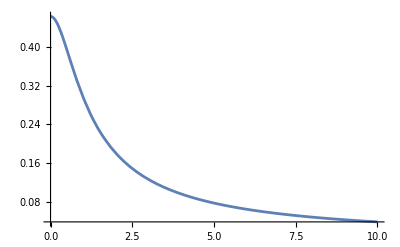

-Graphics3D-

```mathematica
Plot3D[coshint[m, p],{m,0,1},{p,0,10}, AxesLabel->Automatic, PlotRange->All]
```

```mathematica
N[coshint[0.5, 1]]
```

0.295453